# Model with stochastic error

```mathematica
ClearAll["Global`*"];


(*set working directory that plots will go into*)

SetDirectory["\\Users\\jabunce\\Dropbox\\Matsigenka-Mestizo_project_2014\\perception_analysis\\xcult_dynamics"];
(*
SetDirectory["/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics"];
*)


(*Note that A and B in the following equations are the same as Groups S and L, respectively, in the text*)
```

## Functions

```mathematica
(*****************logistic function - increasing*************)
Logistic[x_]:=Module[{},1/(1+Exp[-1*x])];


(*****************Function to simulate phenotype evolution****************)
xcultsim[
matAinit_,(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit_,(*(matrix) initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)
tmax_,(*# sims*)
b_,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c_,(*cost of coordinating using norm that is not personally held*)
a_,(*(vector) probability of assorting to interact with members of your own group, rather than with outgroup {aA,aB}*)
m_,(*cost of having to learn and maintain cross-cultural competence*)
i_,(*identity valuation*)
muA_,(*effect of a power difference on copying between groups*)
var_ (*error variance in phenotype frequency perceptions*)
]:=Module[{},

(*intialize vectors and matrices*)
matA=matAinit;(*matrix of phenotypes in each group*)
matB=matBinit;
matAall=matAinit;(*list holding matrices of all phenotype freqs for group A over time*)
matBall=matBinit;
fitAtilde={{1,1},{1,1}};(*anticipated fitness of phenotypes in group A: {{A11,A1c},{A2c,A22}}*)
fitBtilde={{1,1},{1,1}};
fitAalltilde=fitAtilde;(*matrix holding all anticipated phenotype fitnesses for group A over time*)
fitBalltilde=fitBtilde;



(*simulation*)
For[t=1,t<=tmax,t++,


Clear[pA11,pA1X,pA2X,pA22,
pB11,pB1X,pB2X,pB22,
bA,bB,
wA11,wA1X,wA2X,wA22,
wB11,wB1X,wB2X,wB22,
wA11temp,wA1Xtemp,wA2Xtemp,wA22temp,
wB11temp,wB1Xtemp,wB2Xtemp,wB22temp,
wA11tildetemp,wA1Xtildetemp,wA2Xtildetemp,wA22tildetemp,
wB11tildetemp,wB1Xtildetemp,wB2Xtildetemp,wB22tildetemp,
poA1,poB1,
pAtildetot,pBtildetot];


(* Probability of observing attempts to use norm 1 by group A and norm 2 by group B indivs with in- and out-group *)

(*error variance*)
errvar=var;

poA1in=pA11*(pA11+pA1X+pA2X+pA22)+
pA1X*(pA11+pA1X+1/2*pA2X)+
pA2X*(pA11+1/2*pA1X)+RandomVariate[NormalDistribution[0,errvar],1][[1]];

poA1out=pA11*(pB11+pB1X+pB2X+pB22)+
pA1X*(pB11+pB1X+1/2*pB2X)+
pA2X*(pB11+1/2*pB1X)+RandomVariate[NormalDistribution[0,errvar],1][[1]];


poB2in=pB22*(pB22+pB2X+pB1X+pB11)+
pB2X*(pB22+pB2X+1/2*pB1X)+
pB1X*(pB22+1/2*pB2X)+RandomVariate[NormalDistribution[0,errvar],1][[1]];

poB2out=pB22*(pA22+pA2X+pA1X+pA11)+
pB2X*(pA22+pA2X+1/2*pA1X)+
pB1X*(pA22+1/2*pA2X)+RandomVariate[NormalDistribution[0,errvar],1][[1]];

If[poA1in>1,poA1in=1,If[poA1in<0,poA1in=0]];
If[poA1out>1,poA1out=1,If[poA1out<0,poA1out=0]];
If[poB2in>1,poB2in=1,If[poB2in<0,poB2in=0]];
If[poB2out>1,poB2out=1,If[poB2out<0,poB2out=0]];


(*anticipated phenotype payoffs*)

wA11tildetemp=aA*poA1in+(1-aA)*(1-poB2out)*(1+bA)+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA1Xtildetemp=aA*(poA1in+(1-poA1in)*(1-c))+
(1-aA)*((1-poB2out)*(1+bA)+poB2out*(1+bA-c))-m+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA2Xtildetemp=aA*((1-poA1in)+poA1in*(1-c))+
(1-aA)*(poB2out*(1+bA)+(1-poB2out)*(1+bA-c))-m+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA22tildetemp=aA*(1-poA1in)+(1-aA)*poB2out*(1+bA)+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};



wB11tildetemp=aB*(1-poB2in)+(1-aB)*poA1out*(1+bB)+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB1Xtildetemp=aB*((1-poB2in)+poB2in*(1-c))+
(1-aB)*(poA1out*(1+bB)+(1-poA1out)*(1+bB-c))-m+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB2Xtildetemp=aB*(poB2in+(1-poB2in)*(1-c))+
(1-aB)*((1-poA1out)*(1+bB)+poA1out*(1+bB-c))-m+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB22tildetemp=aB*poB2in+(1-aB)*(1-poA1out)*(1+bB)+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};



(*anticipated total probability of all transitions from uni-cult competence*)

pA11tildetot=Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA11tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA22tildetot=Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA22tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



pB22tildetot=Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB22tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pB11tildetot=Logistic[(muA*(wB11tilde-wB2Xtilde))]*
Logistic[(muA*(wB11tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB11tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



(*new phenotype frequencies after updating*)

pA11prime=aA*pA11*(pA11+pA1X+pA2X+
pA22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)+
(1-aA)*pA11*(pB11+pB1X+pB2X+
pB22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA1Xprime=aA*pA11*pA22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
(1-aA)*pA11*pB22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
aA*pA1X*(pA11+pA1X)+
aA*pA1X*pA2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA1X*pA22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA1X*(pB11+pB1X)+
(1-aA)*pA1X*pB2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA1X*pB22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA2X*pB11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA2X*pB1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA22*pA11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot+
(1-aA)*pA22*pB11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pA22prime=aA*pA22*(pA22+pA2X+pA1X+
pA11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)+
(1-aA)*pA22*(pB22+pB2X+pB1X+
pB11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA2Xprime=1-pA11prime-pA1Xprime-pA22prime;




pB22prime=aB*pB22*(pB22+pB2X+pB1X+
pB11*(Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))])/pB22tildetot)+
(1-aB)*pB22*(pA22+pA2X+pA1X+
pA11*(Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))])/pB22tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pB2Xprime=aB*pB22*pB11*(Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB22tildetot+
(1-aB)*pB22*pA11*(Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB22tildetot+
aB*pB2X*(pB22+pB2X)+
aB*pB2X*pB1X*(1/2*1+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+
aA*pB2X*pB11*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
(1-aB)*pB2X*(pA22+pA2X)+
(1-aB)*pB2X*pA1X*(1/2*1+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+ 
(1-aB)*pB2X*pA11*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
aB*pB1X*pB22*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
aB*pB1X*pB2X*(1/2*0+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+ 
(1-aB)*pB1X*pA22*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
(1-aB)*pB1X*pA2X*(1/2*0+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+
aB*pB11*pB22*(Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB11tildetot+
(1-aB)*pB11*pA22*(Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB11tildetot//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pB11prime=aB*pB11*(pB11+pB1X+pB2X+
pB22*(Logistic[(muA*(wB11tilde-wB1Xtilde))]*
Logistic[(muA*(wB11tilde-wB2Xtilde))])/pB11tildetot)+
(1-aB)*pB11*(pA11+pA1X+pA2X+
pA22*(Logistic[(muA*(wB11tilde-wB1Xtilde))]*
Logistic[(muA*(wB11tilde-wB2Xtilde))])/pB11tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pB1Xprime=1-pB22prime-pB2Xprime-pB11prime;


(*update phenotype and fitness matrices*)
digs=300;

matA = N[{{pA11prime,pA1Xprime},{pA2Xprime,pA22prime}},digs];
matB = N[{{pB11prime,pB1Xprime},{pB2Xprime,pB22prime}},digs];
fitAtilde=N[{{wA11tildetemp,wA1Xtildetemp},{wA2Xtildetemp,wA22tildetemp}},digs];
fitBtilde=N[{{wB11tildetemp,wB1Xtildetemp},{wB2Xtildetemp,wB22tildetemp}},digs];

(*accumulate phenotype freqs and fitnesses across sims*)
matAall=Join[matAall,matA];
matBall=Join[matBall,matB];
fitAalltilde=Join[fitAalltilde, fitAtilde];
fitBalltilde=Join[fitBalltilde, fitBtilde]


];(*for t*)

];(*xcultsim*)
```

## Explore effects of error variance

a Done Group A

a Done Group B

b Done Group A

b Done Group B

c Done Group A

c Done Group B

d Done Group A

d Done Group B

e Done Group A

e Done Group B

f Done Group A

f Done Group B

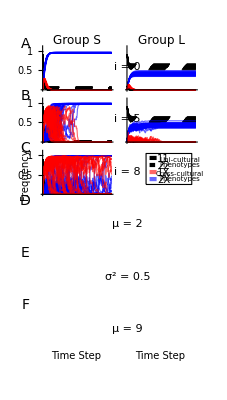

./figures/FigureTrajCerr.pdf

```mathematica
(*explore variance effects*)

(*A***************** i=0 ****************************)

nmax=50; (*number of sample trajectories per phenotype to plot*)
varerr=1/4; (*error variance in phenotype frequency perceptions*)

tmaxval=200; (*number of simulations*)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];


For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=1 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];
](*for n*)

(*
Round[matA11gA,0.01] //MatrixForm
Transpose[Round[matA11gA,0.01]]
*)

figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figaA=Show[figA11,figA22,figA2X,figA1X];

Print["a Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figaB=Show[figB11,figB22,figB2X,figB1X];

Print["a Done Group B"];



(*B******************** i=5 ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=5,(*identity valuation*)
muA=1 ,(*effect of a power difference on copying between groups*)
var=varerr(*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figbA=Show[figA11,figA22,figA2X,figA1X];

Print["b Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figbB=Show[figB11,figB22,figB2X,figB1X];

Print["b Done Group B"];



(*C******************** i=8 ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=8,(*identity valuation*)
muA=1 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figcA=Show[figA11,figA22,figA2X,figA1X];

Print["c Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figcB=Show[figB11,figB22,figB2X,figB1X];

Print["c Done Group B"];



(*D******************** mu=2 ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=5,(*identity valuation*)
muA=2 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figdA=Show[figA11,figA22,figA2X,figA1X];

Print["d Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figdB=Show[figB11,figB22,figB2X,figB1X];

Print["d Done Group B"];



(*E******************** var=1/2 ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=5,(*identity valuation*)
muA=2,(*effect of a power difference on copying between groups*)
var=varerr+1/4 (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figeA=Show[figA11,figA22,figA2X,figA1X];

Print["e Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figeB=Show[figB11,figB22,figB2X,figB1X];

Print["e Done Group B"];



(*F******************** mu=10 ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=10,(*identity valuation*)
muA=9,(*effect of a power difference on copying between groups*)
var=varerr+1/4 (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figfA=Show[figA11,figA22,figA2X,figA1X];

Print["f Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{200,"200"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figfB=Show[figB11,figB22,figB2X,figB1X];

Print["f Done Group B"];


(******************* assemble plots into Figure ****************************)
FigureTrajCerr=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB},{figcA,figcB},{figdA,figdB},
{figeA,figeB},{figfA,figfB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Style["A",14],{20,-30}],
Inset[Style["B",14],{20,-253}],
Inset[Style["C",14],{20,-476}],
Inset[Style["D",14],{20,-699}],
Inset[Style["E",14],{20,-922}],
Inset[Style["F",14],{20,-1145}],
Inset[Rotate[Style["Frequency",10],90Degree],{20,-586}],
Inset[Style["Time Step",10],{235,-1360}],
Inset[Style["Time Step",10],{595,-1360}],

Inset[Row[{Style["i",Italic,10],Style[" = 0",10]}],{397,-130},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 5",10]}],{397,-353},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 8",10]}],{397,-576},{Left,Center}],
Inset[Row[{Style["μ",10],Style[" = 2",10]}],{390,-799},{Left,Center}],
Inset[Row[{Style[Superscript[Style["σ",10],Style["2",8]]],Style[" = 0.5",10]}],{360,-1022},{Left,Center}],
Inset[Row[{Style["μ",10],Style[" = 9",10]}],{390,-1245},{Left,Center}],

x1=350;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{185+x1,-78+y1},{380+x1,-210+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural",7],{330+x1,-105+y1}],
Inset[Style["Phenotypes",7],{330+x1,-125+y1}],
Inset[Style["22",10],{260+x1,-130+y1}],
Inset[Style["1X",10],{260+x1,-160+y1}],
Inset[Style["Cross-cultural",7],{330+x1,-165+y1}],
Inset[Style["Phenotypes",7],{330+x1,-185+y1}],
Inset[Style["2X",10],{260+x1,-190+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{200+x1,-127+y1},{230+x1,-127+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{200+x1,-157+y1},{230+x1,-157+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{200+x1,-187+y1},{230+x1,-187+y1}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)


Export["./figures/FigureTrajCerr.pdf",FigureTrajCerr, "PDF"(*"AllowRasterization"->True,ImageSize->500,ImageResolution->1000*)]
```

## Trajectory Sensitivity

```mathematica
(*trajectory sensitivity analysis*)

(*A***************** no power differences ****************************)

nmax=50; (*number of sample trajectories per phenotype to plot*)
varerr=1/2; (*error variance in phenotype frequency perceptions*)

tmaxval=50; (*number of simulations*)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];


For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2, (*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];
](*for n*)

(*
Round[matA11gA,0.01] //MatrixForm
Transpose[Round[matA11gA,0.01]]
*)

figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figaA=Show[figA11,figA22,figA2X,figA1X];

Print["a Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figaB=Show[figB11,figB22,figB2X,figB1X];

Print["a Done Group B"];



(*B******************** power difference ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figbA=Show[figA11,figA22,figA2X,figA1X];

Print["b Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figbB=Show[figB11,figB22,figB2X,figB1X];

Print["b Done Group B"];



(*C******************** low affinity ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figcA=Show[figA11,figA22,figA2X,figA1X];

Print["c Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figcB=Show[figB11,figB22,figB2X,figB1X];

Print["c Done Group B"];



(*D******************** identity ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figdA=Show[figA11,figA22,figA2X,figA1X];

Print["d Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figdB=Show[figB11,figB22,figB2X,figB1X];

Print["d Done Group B"];



(*E******************** large power difference ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={5,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figeA=Show[figA11,figA22,figA2X,figA1X];

Print["e Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figeB=Show[figB11,figB22,figB2X,figB1X];

Print["e Done Group B"];



(*F******************** high cognitive dissonance ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figfA=Show[figA11,figA22,figA2X,figA1X];

Print["f Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figfB=Show[figB11,figB22,figB2X,figB1X];

Print["f Done Group B"];



(*G******************** high maintenance ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figgA=Show[figA11,figA22,figA2X,figA1X];

Print["g Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,""}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figgB=Show[figB11,figB22,figB2X,figB1X];

Print["g Done Group B"];



(*H******************** high payoff bias ******************)

matA11gA=Transpose[{ConstantArray[0,tmaxval]}];(*list holding matrices of all trajectories for group A over time*)
matA1XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA2XgA=Transpose[{ConstantArray[0,tmaxval]}];
matA22gA=Transpose[{ConstantArray[0,tmaxval]}];
matB11gB=Transpose[{ConstantArray[0,tmaxval]}];
matB1XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB2XgB=Transpose[{ConstantArray[0,tmaxval]}];
matB22gB=Transpose[{ConstantArray[0,tmaxval]}];

For[n=1,n≤nmax,n++,

xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=tmaxval,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=3 ,(*effect of a power difference on copying between groups*)
var=varerr (*error variance in phenotype perceptions*)
];


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

matA11gA=MapThread[Append,{matA11gA,A11gA}];
matA1XgA=MapThread[Append,{matA1XgA,A1XgA}];
matA2XgA=MapThread[Append,{matA2XgA,A2XgA}];
matA22gA=MapThread[Append,{matA22gA,A22gA}];
matB11gB=MapThread[Append,{matB11gB,B11gB}];
matB1XgB=MapThread[Append,{matB1XgB,B1XgB}];
matB2XgB=MapThread[Append,{matB2XgB,B2XgB}];
matB22gB=MapThread[Append,{matB22gB,B22gB}];

Clear[A11gA,A2XgA,A1XgA,A22gA,B11gB,B2XgB,B1XgB,B22gB];

] (*for n*)


figA11=
ListLinePlot[
Transpose[matA11gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA22=
ListLinePlot[
Transpose[matA22gA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA2X=
ListLinePlot[
Transpose[matA2XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

figA1X=
ListLinePlot[
Transpose[matA1XgA[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,""},{0.5,"0.5"},{1,"1"}}}
];

fighA=Show[figA11,figA22,figA2X,figA1X];

Print["h Done Group A"];

figB11=
ListLinePlot[
Transpose[matB11gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB22=
ListLinePlot[
Transpose[matB22gB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB2X=
ListLinePlot[
Transpose[matB2XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Blue,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

figB1X=
ListLinePlot[
Transpose[matB1XgB[[All,2;;]]],
PlotRange->{{0,tmaxval},{-0.01,1.1}},
PlotStyle->{{Red,Opacity[0.6],Thickness[0.002]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,""},{50,"50"}},{{0,"",{0,0}},{0.5,"",{0,0}},{1,"",{0,0}}}}
];

fighB=Show[figB11,figB22,figB2X,figB1X];

Print["h Done Group B"];


(***************** assemble plots into Figure ****************************)
FigureTrajAllerr=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB},{figcA,figcB},{figdA,figdB},
{figeA,figeB},{figfA,figfB},{figgA,figgB},{fighA,fighB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Style["A",14],{20,-30}],
Inset[Style["B",14],{20,-253}],
Inset[Style["C",14],{20,-476}],
Inset[Style["D",14],{20,-699}],
Inset[Style["E",14],{20,-922}],
Inset[Style["F",14],{20,-1145}],
Inset[Style["G",14],{20,-1368}],
Inset[Style["H",14],{20,-1591}],
Inset[Rotate[Style["Frequency",10],90Degree],{20,-1032}],
Inset[Style["Time Step",10],{235,-1795}],
Inset[Style["Time Step",10],{595,-1795}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{415,-353}],
Inset[Style[DownArrow["",Style["a",Italic,10]]],{415,-576}],
Inset[Style[UpArrow["",Style["i",Italic,10]]],{415,-799}],
Inset[Style[UpArrow["","",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{410,-1022}],
Inset[Style[UpArrow["",Style["c",Italic,10]]],{415,-1245}],
Inset[Style[UpArrow["",Style["m",Italic,10]]],{415,-1468}],
Inset[Style[UpArrow["",Style["μ",10]]],{415,-1691}], (*type \[Mu ] w/o the space*)

x1=350;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{185+x1,-78+y1},{380+x1,-210+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural",5],{330+x1,-105+y1}],
Inset[Style["Phenotypes",5],{330+x1,-125+y1}],
Inset[Style["22",10],{260+x1,-130+y1}],
Inset[Style["1X",10],{260+x1,-160+y1}],
Inset[Style["Cross-cultural",5],{330+x1,-165+y1}],
Inset[Style["Phenotypes",5],{330+x1,-185+y1}],
Inset[Style["2X",10],{260+x1,-190+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{200+x1,-127+y1},{230+x1,-127+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{200+x1,-157+y1},{230+x1,-157+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{200+x1,-187+y1},{230+x1,-187+y1}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)


Export["./figures/FigureTrajAllerr.pdf",FigureTrajAllerr, "PDF"(*"AllowRasterization"->True,ImageSize->500,ImageResolution->1000*)]
```

a Done Group A

a Done Group B

b Done Group A

b Done Group B

c Done Group A

c Done Group B

d Done Group A

d Done Group B

e Done Group A

e Done Group B

f Done Group A

f Done Group B

g Done Group A

g Done Group B

h Done Group A

h Done Group B

-Graphics-

./figures/FigureTrajAllerr.pdf